# Hermite Curve

```mathematica
G = {{0,0}, {40,0}, {20,20}, {20,20}};
```

```mathematica
M = {{2, -3, 0, 1}, {-2, 3, 0, 0}, {1, -2, 1, 0}, {1, -1, 0, 0}};
T = {t^3, t^2, t, 1};
```

```mathematica
hermite = Transpose[G].M.Transpose[T];
hermite//MatrixForm
```

(20 t+60 t^2-40 t^3
20 t-60 t^2+40 t^3)

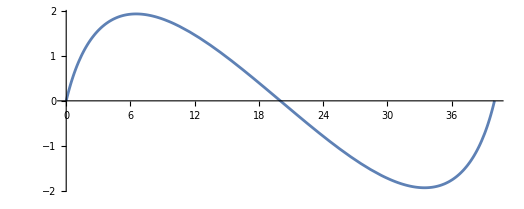

```mathematica
ParametricPlot[hermite /. t->u, {u,0,1}]
```